# Iteration 2: SEIR Model (Incorporating Training Delays)

## Adding Training to a SIR model resulting in dip in farmer productivity

Lets consider a situation where the lord simulation his conscription plan incorporating
a more pratical recruitment plan.

### System Diagram

```mathematica
Graph[{"Susceptible (S)"->"Exposed (E)","Exposed (E)"->"Active (I)","Active (I)"->"Removed (R)"},GraphStyle->"FlowChart",VertexLabels->"Name"]
```

-Graphics-

### Parameter Relationships

```mathematica
Graph[{"Conscript Rate (β)"->"Exposed (E)","Training Rate (σ)"->"Active (I)","Removal Rate (γ)"->"Removed (R)","Susceptible (S)"->"Conscript Rate (β)","Exposed (E)"->"Training Rate (σ)","Active (I)"->"Removal Rate (γ)"},GraphStyle->"CausalLoop",VertexLabels->"Name"]
```

-Graphics-

The training rate 𝜎 governs the flow from Exposed (E) to Active (I).
Conscription and removal rates β and 𝛾 remain critical parameters.

```mathematica
(*RK45 Solver Function*)rk45Solver=Module[{rk45Step},rk45Step[f_,t_,x_,h_]:=Module[{k1,k2,k3,k4,k5,k6,xNext,tNext},k1=h f[t,x];
k2=h f[t+h/4,x+k1/4];
k3=h f[t+3 h/8,x+(3 k1+9 k2)/32];
k4=h f[t+12 h/13,x+(1932 k1-7200 k2+7296 k3)/2197];
k5=h f[t+h,x+(439 k1/216-8 k2+3680 k3/513-845 k4/4104)];
k6=h f[t+h/2,x+(-8 k1/27+2 k2-3544 k3/2565+1859 k4/4104-11 k5/40)];
xNext=x+(16 k1/135+6656 k3/12825+28561 k4/56430-9 k5/50+2 k6/55);
tNext=t+h;
{tNext,xNext}];
rk45Step];

(*SEIR Simulation*)
simulateSEIR=Function[{β,σ,γ,S0,E0,I0,R0,tMax,h},Module[{t=0,x={S0,E0,I0,R0},results={{0,{S0,E0,I0,R0}}},f},f=Function[{t,x},Module[{S=x[[1]],E=x[[2]],I=x[[3]],R=x[[4]],N},N=S+E+I+R;
{-β S I/N,β S I/N-σ E,σ E-γ I,γ I}]];
While[t<tMax,{t,x}=rk45Solver[f,t,x,h];
AppendTo[results,{t,x}];];
results]];

(*Time Series Plot*)plotSEIRTimeSeries=Function[{results},Module[{tValues,SValues,EValues,IValues,RValues},tValues=results[[All,1]];
SValues=results[[All,2,1]];
EValues=results[[All,2,2]];
IValues=results[[All,2,3]];
RValues=results[[All,2,4]];
ListLinePlot[{Transpose[{tValues,SValues}],Transpose[{tValues,EValues}],Transpose[{tValues,IValues}],Transpose[{tValues,RValues}]},PlotStyle->{Blue,Orange,Red,Green},Frame->True,FrameLabel->{"Time","Population"},PlotLegends->{"S (Free Villagers)","E (Selected)","I (Soldiers)","R (Removed)"},ImageSize->Large]]];

(*Phase Space Plot:S vs.I*)
plotSEIRPhaseSpace=Function[{results},Module[{SValues,IValues},SValues=results[[All,2,1]];
IValues=results[[All,2,3]];
ListLinePlot[Transpose[{SValues,IValues}],PlotStyle->Thick,Frame->True,FrameLabel->{"S","I"},ImageSize->Medium]]];

Manipulate[Module[{results},results=simulateSEIR[β,σ,γ,S0,E0,I0,R0,tMax,h];
Column[{Style["SEIR Model in a Medieval Conscription Context",Bold,14],plotSEIRTimeSeries[results],plotSEIRPhaseSpace[results],Style["Interpretation:",Bold,12],"S: villagers free and productive","E: villagers selected but not yet soldiers","I: fully trained soldiers (no longer producing)","R: those who left service and no longer contribute"}]],{{β,0.3,"Conscription Rate (β)"},0.1,1.0,0.05},{{σ,0.2,"Training Rate (σ)"},0.05,0.5,0.05},{{γ,0.1,"Service Exit Rate (γ)"},0.01,0.5,0.01},{{S0,980,"Initial S"},500,1000,10},{{E0,10,"Initial E"},0,50,1},{{I0,10,"Initial I"},1,50,1},{{R0,0,"Initial R"},0,50,1},{{tMax,100,"Total Time"},50,200,10},{{h,0.1,"Step Size"},0.01,1.0,0.01},ControlPlacement->Left,SaveDefinitions->True]
```

## Analysis

### Observation

### Insight

```mathematica
bifurcationPlot2=f|->Module[{sign=D[f,x]>0},Show[ContourPlot[If[sign,1,Null] f==0,{r,0,1},{x,0,15},ContourStyle->Dashed,FrameLabel->{"r","\!\(\*SuperscriptBox[\(x\), \(*\)]\)"}],ContourPlot[If[sign,Null,1] f==0,{r,0,1},{x,0,15}]]];

bifurcationPlot3=f|->Module[{sign=D[f,x]>0},Show[ContourPlot[If[sign,1,Null] f==0,{k,0,15},{x,0,15},ContourStyle->Dashed,FrameLabel->{"k","\!\(\*SuperscriptBox[\(x\), \(*\)]\)"}],ContourPlot[If[sign,Null,1] f==0,{k,0,15},{x,0,15}]]];

Manipulate[bifurcationPlot2[r x (1-x/k)-x^2/(1+x^2)],{{k,10},0,15}]

Manipulate[bifurcationPlot3[r x (1-x/k)-x^2/(1+x^2)],{{r,0.54},0,1}]
```

```mathematica
(*Extended RK45 Solver Function*)rk45Solver=Module[{rk45Step},rk45Step[f_,t_,x_,h_]:=Module[{k1,k2,k3,k4,k5,k6,xNext,tNext},k1=h f[t,x];
k2=h f[t+h/4,x+k1/4];
k3=h f[t+3 h/8,x+(3 k1+9 k2)/32];
k4=h f[t+12 h/13,x+(1932 k1-7200 k2+7296 k3)/2197];
k5=h f[t+h,x+(439 k1/216-8 k2+3680 k3/513-845 k4/4104)];
k6=h f[t+h/2,x+(-8 k1/27+2 k2-3544 k3/2565+1859 k4/4104-11 k5/40)];
xNext=x+(16 k1/135+6656 k3/12825+28561 k4/56430-9 k5/50+2 k6/55);
tNext=t+h;
{tNext,xNext}];
rk45Step];

(*SEIR+Resource Simulation*)
simulateSEIRResource=Function[{β,σ,γ,α,μ,S0,E0,I0,R0,F0,tMax,h},Module[{t=0,x={S0,E0,I0,R0,F0},results={{0,{S0,E0,I0,R0,F0}}},f},f=Function[{t,x},Module[{S=x[[1]],E=x[[2]],I=x[[3]],R=x[[4]],F=x[[5]],N},N=S+E+I+R;
{-β S I/N,(*dS/dt*)β S I/N-σ E,(*dE/dt*)σ E-γ I,(*dI/dt*)γ I,(*dR/dt*)α S-μ (E+I)      (*dF/dt*)}]];
While[t<tMax,{t,x}=rk45Solver[f,t,x,h];
AppendTo[results,{t,x}];];
results]];
(*Time Series Plot for S,E,I,R,and F*)plotSEIRFTimeSeries=Function[{results},Module[{tValues,SValues,EValues,IValues,RValues,FValues},tValues=results[[All,1]];
SValues=results[[All,2,1]];
EValues=results[[All,2,2]];
IValues=results[[All,2,3]];
RValues=results[[All,2,4]];
FValues=results[[All,2,5]];
Column[{ListLinePlot[{Transpose[{tValues,SValues}],Transpose[{tValues,EValues}],Transpose[{tValues,IValues}],Transpose[{tValues,RValues}],Transpose[{tValues,FValues}]},PlotStyle->{Blue,Orange,Red,Green,Purple},Frame->True,FrameLabel->{"Time","Population/Resources"},PlotLegends->{"S (Free)","E (Training)","I (Soldiers)","R (Removed)","F (Resources)"},ImageSize->Large]}]]];
(*Phase Space Plot:S vs I to visualize population dynamics*)plotSEIRFPhaseSpace=Function[{results},Module[{SValues,IValues},SValues=results[[All,2,1]];
IValues=results[[All,2,3]];
ListLinePlot[Transpose[{SValues,IValues}],PlotStyle->Thick,Frame->True,FrameLabel->{"S","I"},ImageSize->Medium]]];
Manipulate[Module[{results},results=simulateSEIRResource[β,σ,γ,α,μ,S0,E0,I0,R0,F0,tMax,h];
Column[{Style["SEIR Model with Resource Dynamics",Bold,14],"This extension includes a resource variable (F). Changes in F represent the availability of food/resources influencing S, E, I dynamics.",plotSEIRFTimeSeries[results],plotSEIRFPhaseSpace[results],Style["Interpretation:",Bold,12],"S: Free villagers producing resources","E: Selected trainees consuming resources","I: Active soldiers also consuming resources","R: Removed from system, no longer contributing","F: Resource level balancing production (by S) and consumption (by E, I)"}]],{{β,0.3,"Conscription Rate (β)"},0.1,1.0,0.05},{{σ,0.2,"Training Rate (σ)"},0.05,0.5,0.05},{{γ,0.1,"Service Exit Rate (γ)"},0.01,0.5,0.01},{{α,1.0,"Resource Prod. Rate (α)"},0.1,3.0,0.1},{{μ,0.5,"Resource Cons. Rate (μ)"},0.1,2.0,0.1},{{S0,980,"Initial S"},500,1000,10},{{E0,10,"Initial E"},0,50,1},{{I0,10,"Initial I"},1,50,1},{{R0,0,"Initial R"},0,50,1},{{F0,100,"Initial F"},50,300,10},{{tMax,100,"Total Time"},50,200,10},{{h,0.1,"Step Size"},0.01,1.0,0.01},ControlPlacement->Left,SaveDefinitions->True]
```

# Bifurcation Due to Policy Changes (reaching)

## Refer to code comments for more nuanced explanations

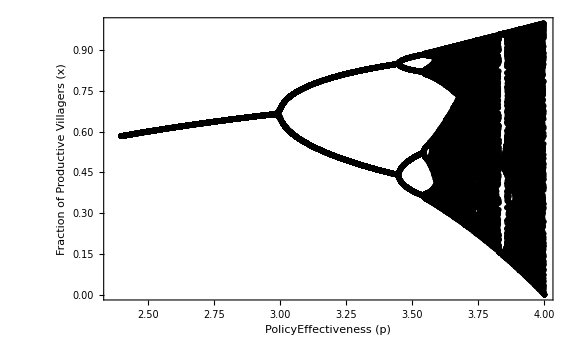

```mathematica
ClearAll["Global`*"];

(*We have called 'r' 'PolicyEffectiveness' to represent how changes in policy (resource management,training incentives,conscription relaxation) affect the productive population fraction.*)

productiveMap[x_,PolicyEffectiveness_]:=PolicyEffectiveness*x*(1-x)

(*x represents the fraction of villagers remaining productive after a season.PolicyEffectiveness (analogous to'r') is a parameter controlled by the lord’s decisions.*)

numIter=200;    (*total iterations per PolicyEffectiveness value*)
discard=100;    (*discard initial transient iterations*)
policyValues=Range[2.4,4,0.002]; (*Explore a range of PolicyEffectiveness values*)

bifData=Reap[Do[Module[{x=0.5},(*We start with a fraction of 0.5 as an initial condition*)
(*Now we let the system settle*)
Do[x=productiveMap[x,p],{numIter}];

(*Record the steady state values after discarding the transient*)
Do[x=productiveMap[x,p];
Sow[{p,x}],
{numIter-discard}]
],
{p,policyValues}]][[2,1]];

(*Now we have bifurcation data of how the fraction x varies as we change PolicyEffectiveness p*)

ListPlot[
bifData,
PlotRange->All,
Frame->True,
FrameLabel->{
"PolicyEffectiveness (p)",
"Fraction of Productive Villagers (x)"},
PlotStyle->{PointSize[0.001],Black},ImageSize->Large,Axes->False]
```